# Parameters:

```mathematica
(*θHVal = 0.25; *)                                 (* AB phase  - Higgs fluctuation *)
Subscript[sin2θ, W] = 0.2312;                           (* Weinberg angle *)
k= 89130;                              (* Warping constant (GeV)*)
Subscript[z, L] =35;                                         (*  Warp factor  = e^(k L_5) *)

ξGauge = 0

Subscript[c, 0] = 0.214075; (**)                                (*Up type quark bulk position*)
Subscript[c, 1] = 0;                                                                         (*Down type quark bulk position*)
Subscript[c, 2] = -0.7;
c0Prime = 0.5224;

μ11 = 0.108;
μ1 = 11.18;

μ11Prime = 0.108;
μ2Tilde = 0.7091;

M = -10^7;
mB = 1.145 * 10^12;
```

0

# Dependents:

```mathematica
Subscript[L, 5]=Log[Subscript[z, L]]/k;                      (* Dimension of 5th dimm y (GeV)^-1 *)
Subscript[m, KK5] = (π k)/(Subscript[z, L] - 1);                                    (* KK5 mass scale (GeV) *)
```

# Mass Spectrum:

EW Bosons:

```mathematica
Subscript[m, W] = (√3 * Sin[Subscript[θ, H]])/(√2 π √Subscript[z, L]) * Subscript[m, KK5]/.{Subscript[θ, H]->0.15}                                           (*W Boson mass*)
Subscript[m, Z@GUT] = Sqrt[12/5] k (Subscript[z, L])^(-3/2)Sin[Subscript[θ, H]]    /.{Subscript[θ, H]->0.15}                   (*Z Boson Mass with unran Sin^2[Subscript[θ, W]] = 3/8 at the GUT scale*)
Subscript[m, Z@TeV] = Subscript[m, W]/Sqrt[1-Subscript[sin2θ, W] ]                                            (*Z Boson Mass with evolved, observed Sin^2[Subscript[θ, W]] = 0.2312 at the TeV scale *)
```

81.0995

99.6527

92.4935

Quarks and Leptons:

```mathematica
muTypeQuark[c0_]:=If[c0< 0.5,
 k/Subscript[z, L] Sqrt[1 - 4 (c0)^2]Sin[Subscript[θ, H]/2],
 k (Subscript[z, L])^(1/2 - Subscript[c, 0])Sqrt[4(c0)^2 - 1]Sin[Subscript[θ, H]/2]
]
mdTypeQuark[c0_, c1_, μ11_, μ1_]:=If[c0<0.5,
k * ((Subscript[z, L])^(c0-c1-1)) * μ11/μ1 Sqrt[(1-2c0)(1+2c1)]Sin[Subscript[θ, H]/2],
k * ((Subscript[z, L])^(-c1-1/2)) * μ11/μ1 Sqrt[(2c0 - 1)(2c1 + 1)Sin[Subscript[θ, H]/2]]
]
meTypeLepton[c2_, c0_, μ11Prime_, μ2Tilde_]:=If[ c2<0.5,
k * ((Subscript[z, L])^(-1+c2-c0)) * μ11Prime/μ2Tilde Sqrt[(2c0 + 1)(1-2c2)]Sin[Subscript[θ, H]/2],
k *  ((Subscript[z, L])^(-1/2 - c0)) * μ11Prime/μ2Tilde Sqrt[(2c0+1)(2c2-1)]Sin[Subscript[θ, H]/2]
]

mνType [mu_, M_, mB_, c0_]:=-(2(mu)^2 *M* ((Subscript[z, L])^(2c0 + 1)))/((2c0 + 1) *mB^2)
```

```mathematica
Print ["Top mass of : ", muTypeQuark[Subscript[c, 0]]/.{Subscript[θ, H]->0.15}, " GeV"]
Print ["Bottom mass of : ",mdTypeQuark[Subscript[c, 0],Subscript[c, 1], μ11, μ1], " GeV"]
Print ["Tau lepton mass of : ",meTypeLepton[Subscript[c, 2], Subscript[c, 0], μ11Prime, μ2Tilde] , " GeV"]
Print ["Tau Neutrino mass of : ",mνType[Subscript[m, t], M, mB, Subscript[c, 0]] * 10^9, " eV"]
Print ["Dark fermion mass of : ", muTypeQuark[c0Prime] , " GeV"]
```

Top mass of : 172.44 GeV

Bottom mass of : 39.8222 Sin[θ_H/2] GeV

Tau lepton mass of : 27.8465 Sin[θ_H/2] GeV

Tau Neutrino mass of : 1.71319×10^-6 m_t^2 eV

Dark fermion mass of : 74554.9 Sin[θ_H/2] GeV

```mathematica
(*Fixing Subscript[c, 0] via top Mass*)
c0Sols = NSolve[{k/Subscript[z, L] Sqrt[1 - 4 (c0)^2]Sin[Subscript[θ, H]/2]==mTop}, c0]/.{ mTop ->172.44, Subscript[θ, H] ->0.15}
```

{{c0→-0.214075},{c0→0.214075}}

```mathematica
NSolve[{(√3 * Sin[Subscript[θ, H]])/(√2 Pi √Subscript[z, L]) *(Pi k)/(Subscript[z, L] - 1)==80.385}, k]
kSoln =  80.385 / ((√3 * Sin[Subscript[θ, H]])/(√2 π √Subscript[z, L]) *π/(Subscript[z, L] - 1));
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{θ_H→0.148669}}

# Integrals and Bessel Functions combos

```mathematica
IntIfct[Q_, f_, q_]:= q^3 Log[1+Q*f ];(*(k/Subscript[z, L])^4/(4Pi)^2 NIntegrate*)
FHat[α_, β_, u_, v_]:=BesselI[α, u] * BesselK[β, v] - Exp[-ⅈ(α - β ) * Pi] * BesselK[α,u] * BesselI[β,v];
FHatcPM[q_, c_, pm1_, pm2_]:=FHat[ c + pm1*1/2, c+pm2*1/2, (q/Subscript[z, L]), q  ]
```

# The Q’s:

```mathematica
Q0[q_, c_]:= Subscript[z, L]/q^2 * 1/(FHatcPM[q, c, 1, 1]*FHatcPM[q, c, -1, -1]);

Qii[q_,c0_,c1_,μ1_, μ11_]:=Subscript[z, L]/q^2*( FHatcPM[q,c0,1, 1]*FHatcPM[q,c0,-1, -1] + (μ1^2 *FHatcPM[q,c0,-1, -1]*FHatcPM[q,c0,-1, 1]*FHatcPM[q,c1,1, 1]*FHatcPM[q,c1,-1, 1])/(μ11^2 * (FHatcPM[q,c1,-1, 1])^2 +( FHatcPM[q,c1,1, 1])^2) )^(-1);

Qiii[q_,c0_,c2_,μ2Tilde_, μ11Prime_]:= Subscript[z, L]/q^2*(FHatcPM[q,c0,1, 1] * FHatcPM[q,c0,-1, -1]  + (μ2Tilde^2*FHatcPM[q,c0,1, 1]*FHatcPM[q,c0,1, -1]*FHatcPM[q,c2,-1, -1]*FHatcPM[q,c2,1, -1])/(μ11Prime^2 * (FHatcPM[q,c2,1, -1])^2 + (FHatcPM[q,c2,-1, -1])^2) )^(-1)  ;


Qiv1Aux[q_,c0_,mB_, M_ ]:= Subscript[z, L]/q^2*(FHatcPM[q,c0,1, 1] * FHatcPM[q,c0,-1, -1]  + (ⅈ* mB^2 / k^2)/(2(ⅈ q (Subscript[z, L])^(-1) + M/k))*FHatcPM[q,c0,-1, 1]*FHatcPM[q,c0,-1, -1])^(-1);
Qiv1[QAux_, θH_]:=Simplify[(QAux + Conjugate[QAux])] * (Sin[1/2 θH])^2 + Simplify[QAux * Conjugate[QAux]] * (Sin[1/2 θH])^4;


h1[q_, θH_, μ11Prime_, c2_] :=(1-μ11Prime^2)(2 * q^2/Subscript[z, L](1+μ11Prime^2) * FHatcPM[q,c2,1, 1]*FHatcPM[q,c2,-1, -1] + 2 μ11Prime^2 + (1-μ11Prime^2)*(Sin[θH])^2 ) * (Sin[θH])^2;
h2[q_,  μ11Prime_, c2_]:=(Subscript[z, L])^2/q^4* μ11Prime^4 + 2 μ11Prime^4 * (Subscript[z, L])/q^2*FHatcPM[q,c2,1, 1]*FHatcPM[q,c2,-1, -1] + (1+μ11Prime^4)(FHatcPM[q,c2,1, 1]*FHatcPM[q,c2,-1, -1])^2 + μ11Prime^2( (FHatcPM[q,c2,-1, 1]*FHatcPM[q,c2,-1, -1])^2 + (FHatcPM[q,c2,1, -1]*FHatcPM[q,c2,1, 1])^2 );
Qiv2[q_, θH_, μ11Prime_, c2_]:=(Subscript[z, L])^2/q^4 * h1[q, θH, μ11Prime, c2]/h2[q, μ11Prime, c2];

IntConst = N[(k/Subscript[z, L])^4/(4π)^2];
fθH1[θH_]:=(Sin[θH/2])^2

complexDecider[Veff_]:=If[
TrueQ[Head @ Veff==Complex],
Print["Complex Potential with magnitude:   ", Abs[Veff], "\n    Real part of     : ", Re[Veff],  "\n    Complex part of  : ", Im[Veff], "\n"] ,
Print["Real Potential with magnitude :  ",Veff, "\n"]
]
```

# Effective potential V_eff[θ_H]

### Fermion contributions

```mathematica
Subscript[V, eff(i)FCT] = Simplify[ -12 *IntConst *  IntIfct[Q0[q, Subscript[c, 0]], fθH1[Subscript[θ, H]], q], {Subscript[c, 0]∈Reals, q∈Reals, Subscript[θ, H]∈Reals}] ;
Subscript[V, eff(i)] =  NIntegrate [Subscript[V, eff(i)FCT] /.{Subscript[θ, H]->θHVal}, {q , 0, ∞}];
Print[Style["V_(eff (i)) contribution:", FontSize->15, FontColor->Red]]
complexDecider[Subscript[V, eff(i)]]
(**************************************************************************)

Subscript[V, eff(ii)FCT] =Simplify[ -12 * IntConst *IntIfct[Qii[q, Subscript[c, 0], Subscript[c, 1], μ1, μ11], fθH1[Subscript[θ, H]], q ], { {q, Subscript[c, 0], Subscript[c, 1], μ1, μ11, Subscript[θ, H]}∈Reals}] ;
Subscript[V, eff(ii)] =  NIntegrate [Subscript[V, eff(ii)FCT] /.{Subscript[θ, H]->θHVal}, {q , 0, ∞}];
Print[Style["V_(eff (ii)) contribution:", FontSize->15, FontColor->Red]]
complexDecider[Subscript[V, eff(ii)]]
(**************************************************************************)

Subscript[V, eff(iii)FCT] = Simplify[-4 * IntConst * IntIfct[ Qiii[q, Subscript[c, 0], Subscript[c, 2], μ2Tilde, μ11Prime],fθH1[Subscript[θ, H]], q ] ,  {{q, Subscript[c, 0], Subscript[c, 2], μ2Tilde, μ11Prime, Subscript[θ, H]}∈Reals} ];
Subscript[V, eff(iii)] =  NIntegrate [Subscript[V, eff(iii)FCT] /.{Subscript[θ, H]->θHVal}, {q , 0, ∞}];
Print[Style["V_(eff (iii)) contribution:", FontSize->15, FontColor->Red]]
complexDecider[Subscript[V, eff(iii)]]

(**************************************************************************)
Subscript[V, eff(iv1)FCT] = Simplify[-4/2 * IntConst * IntIfct[ Qiv1[ Qiv1Aux[q, Subscript[c, 0], mB, M], Subscript[θ, H] ] , 1, q] ,  {{q, Subscript[c, 0],mB, M,  Subscript[θ, H]}∈Reals} ];
Subscript[V, eff(iv1)] =  NIntegrate [Subscript[V, eff(iv1)FCT] /.{Subscript[θ, H]->θHVal}, {q , 0, ∞}];
Print[Style["V_(eff (iv1)) contribution:", FontSize->15, FontColor->Red]]
complexDecider[Subscript[V, eff(iv1)]]


(**************************************************************************)
Subscript[V, eff(iv2)FCT] =Simplify[-4 * IntConst * IntIfct[ Qiv2[q, Subscript[θ, H], μ11Prime, Subscript[c, 2]], 1, q] ,{{q, μ11Prime, Subscript[c, 2] ,  Subscript[θ, H]}∈Reals} ];
Subscript[V, eff(iv2)] =  NIntegrate [Subscript[V, eff(iv2)FCT] /.{Subscript[θ, H]->θHVal}, {q , 0, ∞}];
Print[Style["V_(eff (iv2)) contribution:", FontSize->15, FontColor->Red]]
complexDecider[Subscript[V, eff(iv2)]]



(**************************************************************************)
Subscript[V, eff(v)FCT] =Simplify[-32 * IntConst * IntIfct[ Q0[q, c0Prime], (Cos[Subscript[θ, H]/2])^2, q] ,{{q, c0Prime,  Subscript[θ, H]}∈Reals} ];
Subscript[V, eff(v)] =  NIntegrate [Subscript[V, eff(v)FCT] /.{Subscript[θ, H]->θHVal}, {q , 0, ∞}];
Print[Style["V_(eff (v)) contribution:", FontSize->15, FontColor->Red]]
complexDecider[Subscript[V, eff(v)]]
```

V_(eff (i)) contribution:

Real Potential with magnitude :  -3.24792×10^10

V_(eff (ii)) contribution:

Complex Potential with magnitude:   4.46008×10^8
    Real part of     : -4.46008×10^8
    Complex part of  : -4.78082×10^-8

V_(eff (iii)) contribution:

Complex Potential with magnitude:   9.51965×10^9
    Real part of     : -9.51965×10^9
    Complex part of  : 1.561×10^-7

V_(eff (iv1)) contribution:

Complex Potential with magnitude:   1.48035×10^-19
    Real part of     : -6.35659×10^-49
    Complex part of  : 1.48035×10^-19

V_(eff (iv2)) contribution:

Complex Potential with magnitude:   1.19042×10^10
    Real part of     : -1.19042×10^10
    Complex part of  : -1.52148×10^-6

V_(eff (v)) contribution:

Real Potential with magnitude :  -8.00289×10^12

### Boson contributions

```mathematica
(**************************************************************************)
Subscript[V, eff(Wpm)FCT] =Simplify[2(3-ξGauge^2) * IntConst * IntIfct[1/2*Q0[q, 1], (Sin[Subscript[θ, H]])^2,q] ,{{q,  Subscript[θ, H]}∈Reals}  ] ;
Subscript[V, eff(Wpm)] =  NIntegrate [Subscript[V, eff(Wpm)FCT] /.{Subscript[θ, H]->θHVal}, {q , 0, ∞}];
Print[Style["V_(eff (Wpm)) contribution:", FontSize->15, FontColor->Red]]
complexDecider[Subscript[V, eff(Wpm)]]


(**************************************************************************)
Subscript[V, eff(Z)FCT] = Simplify [(3-ξGauge^2) * IntConst * IntIfct[Q0[q, 1]/(2(1-Subscript[sin2θ, W])),(Sin[Subscript[θ, H]])^2,q],{{q,  Subscript[θ, H]}∈Reals }];
Subscript[V, eff(Z)] =  NIntegrate [Subscript[V, eff(Z)FCT] /.{Subscript[θ, H]->θHVal}, {q , 0, ∞}];
Print[Style["V_(eff (Z)) contribution:", FontSize->15, FontColor->Red]]
complexDecider[Subscript[V, eff(Z)]]



(**************************************************************************)
Subscript[V, eff(Az)FCT] =Simplify[3 ξGauge^2 * IntConst *  IntIfct[ Q0[q, 1],(Sin[Subscript[θ, H]])^2,q ],{{q,  Subscript[θ, H]}∈Reals } ];
Subscript[V, eff(Az)] =  NIntegrate [Subscript[V, eff(Az)FCT] /.{Subscript[θ, H]->θHVal}, {q , 0, ∞}];
Print[Style["V_(eff (Az)) contribution:", FontSize->15, FontColor->Red]]
complexDecider[Subscript[V, eff(Az)]]

(**************************************************************************)
```

V_(eff (Wpm)) contribution:

Real Potential with magnitude :  3.63228×10^9

V_(eff (Z)) contribution:

Real Potential with magnitude :  2.36182×10^9

V_(eff (Az)) contribution:

Real Potential with magnitude :  0.

### Full Effective Potential

-8.13607×10^12-0.0000436644 ⅈ

{θHLocal→0.884699}

Higgs mass of :     614.026 (GeV)

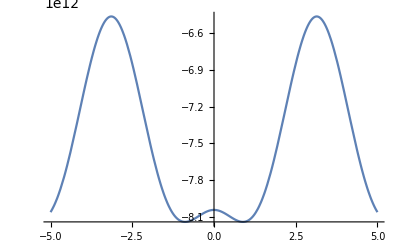

```mathematica
Subscript[V, eff(Fermion)FCT] = Subscript[V, eff(i)FCT] +Subscript[V, eff(ii)FCT] + Subscript[V, eff(iii)FCT]+Subscript[V, eff(iv1)FCT]+Subscript[V, eff(iv2)FCT]+Subscript[V, eff(v)FCT];
Subscript[V, eff(Boson)FCT]=Subscript[V, eff(Wpm)FCT] +Subscript[V, eff(Z)FCT] + Subscript[V, eff(Az)FCT];
Subscript[V, effFCT] = Subscript[V, eff(Fermion)FCT] + Subscript[V, eff(Boson)FCT];

Subscript[V, eff] = NIntegrate [Subscript[V, effFCT] /.{Subscript[θ, H]->θHVal}, {q, 0, ∞}]


θHMinRule = FindMinimum[NIntegrate [Subscript[V, effFCT] /.{Subscript[θ, H]->θHLocal}, {q, 0, ∞}], {θHLocal,0,2 }  ][[2]]
Subscript[m, H] = Sqrt[1/fH^2 * NIntegrate [HiggsDeriv /.{Subscript[θ, H] ->θHLocal/. θHMinRule}, {q, 0, ∞}]/.{fH -> 1.462*10^3}];

Print["Higgs mass of :     ", Abs[Subscript[m, H]], " (GeV)"]
Plot[NIntegrate [Subscript[V, effFCT] /.{Subscript[θ, H]->θHVal}, {q, 0, ∞}]  , {θHVal, -5,5}]
```

```mathematica
.
```

```mathematica
For [θHVal = 0.7  , θHVal ≤ 1, θHVal += 0.01,

HiggsDeriv = D[Subscript[V, effFCT], {Subscript[θ, H],2}](*/.{Subscript[θ, H]->θHVal}*);
Subscript[m, H] = Sqrt[1/fH^2 * NIntegrate [HiggsDeriv /.{Subscript[θ, H]->θHVal}, {q, 0, ∞}]/.{fH -> 1.462*10^3}];

Print["Higgs mass of :     ", Abs[Subscript[m, H]], " (GeV)"]]

(*Plot[1/fH^2 * NIntegrate [HiggsDeriv /.{Subscript[θ, H]->θHVal}, {q, 0, ∞}]/.{fH -> 1.462*10^3}, {θHVal, -5, 5}]*)
```

```mathematica
Print[Style["\nSpin 0,1 contributions", FontSize->20, FontColor->Red]]
Print["W^± Tower contribution of             : ", Subscript[V, eff(Wpm)] , "  (GeV)^4"]
Print["Z^0 Tower contribution of             : ", Subscript[V, eff(Z)] , "  (GeV)^4"]
Print["A_z^a  contribution of                 : ", Subscript[V, eff(Az)] , "  (GeV)^4"]

Print[Style["\nSpin 1/2 contributions", FontSize->20, FontColor->Red]]
Print ["Bulk Up Type Quark (Top) contribution of :                     ", Subscript[V, eff(i)], " (GeV)^4"];
Print ["Bulk Down Type Quark (Top) contribution of :                   ", Subscript[V, eff(ii)], " (GeV)^4"];
Print ["Bulk Charged Lepton (Tau) Fermion contribution of :            ", Subscript[V, eff(iii)], " (GeV)^4"];
Print ["Bulk Neutrino (Tau) Fermion contribution --1-- of :            ", Subscript[V, eff(iv1)], " (GeV)^4"];
Print ["Bulk Neutrino (Tau) Fermion contribution --2-- of :            ", Subscript[V, eff(iv2)], " (GeV)^4"];
Print ["Dark fermion contribution of :                                 ", Subscript[V, eff(v)], " (GeV)^4"];
```

```mathematica
Needs["CCodeGenerator`"]
zL =35;
k=88904;
Print[(1/4(1-((172.44 *zL)/(k * Sin[0.15/2]))^2))^(1/2)]
c=Compile[{{Print[(1/4(1-((172.44 *zL)/(k * Sin[0.15/2]))^2))^(1/2)]}},zL =35;k=88904;];
file=CCodeGenerate[c,"fun"]
```

0.211633

CCodeGenerate::wmreq: The expression Function[{Print$738},zL=35] requires Mathematica to be evaluated.   The function will be generated but can be expected to fail with a nonzero error code when executed.

fun.c

```mathematica
FilePrint[file]
```

#include "math.h"

#include "WolframRTL.h"

static WolframCompileLibrary_Functions funStructCompile;

static void * E0 = 0;

static void * E1 = 0;


static mint I0_0;

static mint I0_1;

static mbool initialize = 1;

#include "fun.h"

DLLEXPORT int Initialize_fun(WolframLibraryData libData)
{
if( initialize)
{
funStructCompile = libData->compileLibraryFunctions;
I0_0 = (mint) 35;
I0_1 = (mint) 88904;
{
E0 = funStructCompile->getExpressionFunctionPointer(libData, "Hold[Function[List[Print$738], Set[zL, 35]]]");
}
if( E0 == 0)
{
return LIBRARY_FUNCTION_ERROR;
}
{
E1 = funStructCompile->getExpressionFunctionPointer(libData, "Hold[Function[List[Print$738], Set[k, 88904]]]");
}
if( E1 == 0)
{
return LIBRARY_FUNCTION_ERROR;
}
initialize = 0;
}
return 0;
}

DLLEXPORT void Uninitialize_fun(WolframLibraryData libData)
{
if( !initialize)
{
initialize = 1;
}
}

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, void *Res)
{
mreal R0_0;
int err = 0;
R0_0 = A1;
{
int S0[1];
void * S1[1];
S0[0] = 3;
S1[0] = (void*) (&R0_0);
err = funStructCompile->evaluateFunctionExpression(libData, E0, 0, 0, 1, S0, S1, 6, 0, 0);
if( err)
{
goto error_label;
}
}
{
int S0[1];
void * S1[1];
S0[0] = 3;
S1[0] = (void*) (&R0_0);
err = funStructCompile->evaluateFunctionExpression(libData, E1, 0, 0, 1, S0, S1, 6, 0, 0);
if( err)
{
goto error_label;
}
}
error_label:
funStructCompile->WolframLibraryData_cleanUp(libData, 1);
return err;
}

```mathematica
Solve[mTop == (k/zL)^(-1/2 - c0Local)*Sqrt[4*c0Local^2-1]*Sin[θH/2], c0Local]
```

$Aborted